In terms of analysis, it will be most helpful, I think, to work with increasingly complex subsets of the full model. The first submodel is the model without parasites.

```mathematica
Srate=3 γ (α^(1/3) Linf S^(2/3)-S);
```

```mathematica
dG=Imax S-ρ G
dC=ρ (1-eA) G-ρ C
dS=Srate
dR=eR (ρ eA G-(m+mc k)(S+R)-eG Srate)
```

Imax S-G ρ

-C ρ+(1-eA) G ρ

3 (-S+Linf S^(2/3) α^(1/3)) γ

eR (-(m+k mc) (R+S)-3 eG (-S+Linf S^(2/3) α^(1/3)) γ+eA G ρ)

We can compute S^*, the structural volume at equilibrium, analytically, to be equal to S^*=α (L_∞)^3. Given this, what are the other equilibria?
G^*=(ι_max S^*)/ρ
C^*=(1-ϵ_A) (ι_max S^*)/ρ
R^*=((ϵ_A ι_max)/(m+k m_c)-1)S^*
Note that this conclusion is unrealistic, as it suggests that, at equilibrium, the ratio of structure to reserves, R^*/S^*=(ϵ_A ι_max)/(m+k m_c)-1. In order for this to be at or near 0.2-0.3, ι_max and m must be of similar magnitude. This makes no biological sense, as they should be more like an order of magnitude different from one another.

We address this problem mathematically by considering condition-dependent ingestion: the animal has a target R/S ratio that it wishes to maintain; when it is below this condition, it accelerates ingestion rate; when it is above this condition, ingestion rate drops. You can incorporate that into the following model:

```mathematica
dG=(Imax S^(2/3))/(1+Exp[η (R/S-θ)])-ρ G
dC=ρ (1-eA) G-ρ C
dS=Srate
dR=eR (ρ eA G-(m+mc k)(S+R)-eG Srate)
```

The equilibrium R depends on the equilibrium gut biomass, as above.

```mathematica
Assuming[Linf>0&&α>0,Simplify[Solve[dR==0,R]/.S->α Linf^3]]/.α->S/Linf^3
```

{{R→(-(m+k mc) S+eA G ρ)/(m+k mc)}}

You can use this to find an expression for R/S, but it doesn’t really help you much. You still get stuck. Suffice it to say that, at equilibrium, there will be some value of R/S that will be larger than θ, and this will cause the ingestion rate to be slightly smaller than ι_max.

```mathematica
pars={Imax->2,
θ->1/3.93,
ρ->2,
η->10,
eA->0.85,
eG->1,
eR->1,
eI->10^-5,
Linf->2.94,
α->1,
γ->0.02,
m->0.2,
mc->0.03,
mi->0.03,
k->4.9 10^-5};
```

Numerical simulations with the above parameter values produce a mouse that ends up with an R/S=0.277777. Given these parameter values, that means that the effective ingestion rate of such a mouse is:

```mathematica
Imax/(1+Exp[η (R/S-θ)])/.pars/.R->0.277777 S
```

0.883905

Because we are considering parasites of the colon, structure and reserves will both settle down to this ratio if the parasite does not provoke an immune response. Let’s consider that unrealistic case to help guide the choice of parameter values for the parasite. The ingestion rate is replaced by the effective ingestion rate calculated above:

```mathematica
dG=Ieff S-ρ G;
dC=ρ (1-eA) G-ρ C-(σ C P)/(H+C);
dP=eP (σ C P)/(H+C)-μ P;
Eq1=Solve[{dG,dC,dP}==0,{G,C,P}]
```

{{G→(Ieff S)/ρ,C→(Ieff S-eA Ieff S)/ρ,P→0},{G→(Ieff S)/ρ,C→-(H μ)/(μ-eP σ),P→(eP (Ieff S μ-eA Ieff S μ+H μ ρ-eP Ieff S σ+eA eP Ieff S σ))/(μ (μ-eP σ))}}

It is clear that the parasite will set the total biomass of the colon. Given what the simulations suggest is a reasonable amount of food in the colon (0.57 g), we want to choose these parameter to make this value make sense. However, we also want to ensure that we have a reasonable biomass of parasites as well. What is reasonable? Well, some old data on infection of rats with tapeworm (Hymenolepis) suggests that a chronic tapeworm infection has worm biomass of ~100 mg (0.1 g). So, not much.

```mathematica
Eq1⟦2⟧/.{Ieff->0.27777,S->α Linf^3}/.pars
Pstar=(Eq1⟦2⟧/.{Ieff->0.27777,S->α Linf^3}/.pars)[[3]][[2]];
Pstar==eP/μ((1.0588113524520004)-2 (-(H μ)/(μ-eP σ)))//Simplify
```

{G→3.52937,C→-(H μ)/(μ-eP σ),P→(eP (1.05881 μ+2 H μ-1.05881 eP σ))/(μ (μ-eP σ))}

True

Let’s look a little more closely: you can show that the equilibrium P^*=ϵ_P/μ(1.06-2 C^*), and C^*=H/(ϵ_P/μ σ-1). So what is critical is not either ϵ_P or μ, but rather their ratio. That is useful to know. In particular, if μ < ϵ_P, which seems reasonable to me, then the only way for P^* to be small is for C^* to be large - near 0.53, which is essentially the colon biomass in the absence of infection.  

Considering that we want C^* to be fairly low - the parasite should eat most of what is there in the absence of any immune regulation - then then ϵ_P/μ should be small, which would require μ > ϵ_P. This is one of those mathematical realities that feels biologically wrong. 

Maybe C^* should not be so small. Let’s imagine choosing parameters such that C^* is half what it would be normally, so about 0.25. Then to get P^*=0.1, you would need ϵ_P/μ=0.1/(1.06-2 (0.25))=0.18, that is ϵ_P=0.18 μ. To get C^*=0.25, I need to choose H and σ such that 0.25(0.15 σ - 1) = H. 

Here is a set of parameters that seems to produce something reasonable.

```mathematica
Eq1⟦2⟧/.{Ieff->0.27777,S->α Linf^3}/.pars/.{eP->0.15, μ->1, σ->10, H->0.1}
```

{G→3.52937,C→0.2,P→0.0988217}

```mathematica
pars={Imax->2,θ->0.2544529262086514,ρ->2,η->10,eA->0.85,eG->1,eR->1,eI->1/100000,Linf->2.94,α->1,γ->0.02,m->0.2,mc->0.03,mi->0.03,k->0.000049,eP->0.15, μ->1, σ->10, H->0.1};
```

Okay, the next step (really, the final step analytically) is to look at what happens when you add only a constitutive immune response. Again, this has the advantage of not affecting either S or R. All that we need to do is add in the effect of the immune response on the parasite.

```mathematica
dG=Ieff S-ρ G;
dC=ρ (1-eA) G-ρ C-(σ C P)/(H+C);
dP=eP (σ C P)/(H+C)-μ P-μc P Ii;
Eq2=Solve[{dG,dC,dP}==0,{G,C,P}]
```

{{G→(Ieff S)/ρ,C→(Ieff S-eA Ieff S)/ρ,P→0},{G→(Ieff S)/ρ,C→-(H (μ+Ii μc))/(μ+Ii μc-eP σ),P→(eP (Ieff S μ-eA Ieff S μ+Ieff Ii S μc-eA Ieff Ii S μc+H μ ρ+H Ii μc ρ-eP Ieff S σ+eA eP Ieff S σ))/((μ+Ii μc) (μ+Ii μc-eP σ))}}

Okay, let’s look at this a bit more carefully. In order for C^* to be positive, it must be the case that I_i μ_i<0.5.

```mathematica
Eq2⟦2⟧/.pars
```

{G→(Ieff S)/2,C→-(0.1 (1+Ii μc))/(-0.5+Ii μc),P→(0.15 (0.2-0.075 Ieff S+0.2 Ii μc+0.15 Ieff Ii S μc))/((-0.5+Ii μc) (1+Ii μc))}

But actually, for an adult, I know exactly how big I_i is, because I_i=k(S+R); a healthy mouse, according to the simulation, has a total biomass of ~32g. Based on Sarah’s mouse data, k = 4.9e-5, so I_i=0.0016. Here is a range of μ_c values that produce C^* values between the value induced by parasites on their own and the parasite-free equilibrium, and P^* values less than the value attained by the parasite on its own. So, a μ_c=100 seems to work fairly well.

```mathematica
Table[Eq2⟦2⟧/.{Ieff->0.27777,S->α Linf^3}/.pars/.{Ii->0.0016} , {μc, 10,150, 10}]
```

{{G→3.52937,C→0.209917,P→0.0943371},{G→3.52937,C→0.220513,P→0.0897944},{G→3.52937,C→0.231858,P→0.0851757},{G→3.52937,C→0.244037,P→0.0804612},{G→3.52937,C→0.257143,P→0.0756286},{G→3.52937,C→0.271287,P→0.0706529},{G→3.52937,C→0.286598,P→0.0655057},{G→3.52937,C→0.303226,P→0.0601542},{G→3.52937,C→0.321348,P→0.0545605},{G→3.52937,C→0.341176,P→0.04868},{G→3.52937,C→0.362963,P→0.0424599},{G→3.52937,C→0.387013,P→0.0358371},{G→3.52937,C→0.413699,P→0.0287352},{G→3.52937,C→0.443478,P→0.0210606},{G→3.52937,C→0.476923,P→0.0126974}}

### Analytical results with P_3 parasites

#### Original model

```mathematica
Srate=3 γ (α^(1/3) Smax^(1/3) S^(2/3)-S);
Ic=c (S+R);
(* maintenance cost for induced immune cells *)
M=mw (S+R)+mc Ic+mI Ii; 

(* State variable dynamics *)
dG=(Imax S^(2/3) F)/(1+Exp[η (R/S-θ)])-ρ G;
dC=ρ (1-eA) G-ρ C;
(* Note that the host does not compensate for the parasite's consumption of structure with extra energy allocation in this model *) 
dS=Srate-(σ P3 S)/(hS+S);
dR=eR (ρ eA G-M-eG Srate-b R P3);
dIi=eI b R P3-muI Ii;
dP3=eP (σ P3 S)/(hS+S)-muP P3-nuC Ic P3-nuI Ii P3;
```

```mathematica
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,Smax->25,F->1.5,Imax->0.9,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.8,eP->1,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
```

I can’t solve for all of these variables simultaneously.

```mathematica
Solve[{dG==0,dC==0,dS==0,dR==0,dIi==0,dP3==0}/.pars,{G,C,W,R,Ii,P3}]
```

$Aborted

However, given the way parasitism is modeled, we can do some simplification. In particular, I don’t need to model the dynamics of food in the colon. Also, once the host has reached its terminal size (shown below), I can simplify the notation a bit by eliminating some other things (notice that in the current model, the host isn’t doing anything to compensate for the loss of structure, whereas we had previously discussed

```mathematica
Solve[Srate==0,S]
```

{{S→0},{S→Smax α}}

Here is the ODE model that can be numerically solved:

```mathematica
Srate=3 γ (α^(1/3) Smax^(1/3) S[t]^(2/3)-S[t]);
Ic=c (S[t]+R[t]);
(* maintenance cost for induced immune cells *)
M=mw (S[t]+R[t])+mc Ic+mI Ii[t]; 

(* State variable dynamics *)
dG=(Imax S[t]^(2/3) F)/(1+Exp[η (R[t]/S[t]-θ)])-ρ G[t];
(* Note that the host does not compensate for the parasite's consumption of structure with extra energy allocation in this model *) 
dS=Srate-(σ P3[t] S[t])/(hS+S[t]);
dCc=ρ (1-eA) G[t]-ρ Cc[t];
dR=eR (ρ eA G[t]-M-eG Srate-b R[t] P3[t]);
dIi=eI b R[t] P3[t]-muI Ii[t];
dP3=(eP σ P3[t] S[t])/(hS+S[t])-muP P3[t]-nuC Ic P3[t]-nuI Ii[t] P3[t];
```

Parameters:

```mathematica
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,Smax->25,F->1.5,Imax->0.9,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.5,eP->0.5,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
```

Solution #1: gives a biologially reasonable solution with a low parasite biomass

```mathematica
TT=500;
soln1=NDSolve[({G'[t]==dG,
S'[t]==dS,
Cc'[t]==dCc,
R'[t]==dR,
Ii'[t]==dIi,
P3'[t]==dP3,
G[0]==0.001,Cc[0]==0.001,S[0]==10,R[0]==1,Ii[0]==0.1,P3[0]==1}/.pars), {G,Cc,S,R,Ii,P3},{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{G[TT],Cc[TT],S[TT],R[TT],Ii[TT],P3[TT]}/.soln1
```

{{3.43471,1.71735,23.7923,4.83246,2.38406,0.0493342}}

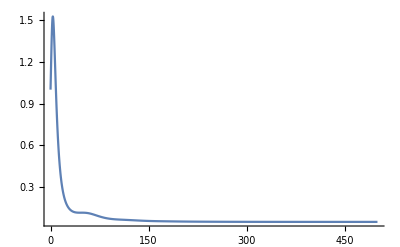

```mathematica
Plot[Evaluate[P3[t]/.soln1],{t,0,TT},PlotRange->All]
```

Solution #2: gives a biologially UNreasonable solution with a high parasite biomass

{{0.0449256,0.0224634,0.0351788,0.00707397,0.0697191,0.984467}}

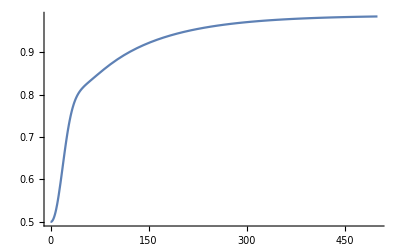

```mathematica
soln2=NDSolve[({G'[t]==dG,
S'[t]==dS,
Cc'[t]==dCc,
R'[t]==dR,
Ii'[t]==dIi,
P3'[t]==dP3,
G[0]==0.01,Cc[0]==0.01,S[0]==0.01,R[0]==0.01,Ii[0]==0.01,P3[0]==0.5}/.pars), {G,Cc,S,R,Ii,P3},{t,0,TT}];
{G[TT],Cc[TT],S[TT],R[TT],Ii[TT],P3[TT]}/.soln2
Plot[Evaluate[P3[t]/.soln2],{t,0,500},PlotRange->All]
```

#### Simplified model that can analytically solved (hopefully)

Get rid of compensatory feeding:

```mathematica
Srate=3 γ (α^(1/3) Smax^(1/3) S[t]^(2/3)-S[t]);
Ic=c (S[t]+R[t]);
(* maintenance cost for induced immune cells *)
M=mw (S[t]+R[t])+mc Ic+mI Ii[t]; 

(* State variable dynamics *)
dG=Imax S[t]^(2/3) F-ρ G[t];
(* Note that the host does not compensate for the parasite's consumption of structure with extra energy allocation in this model *) 
dS=Srate-(σ P3[t] S[t])/(hS+S[t]);
dCc=ρ (1-eA) G[t]-ρ Cc[t];
dR=eR (ρ eA G[t]-M-eG Srate-b R[t] P3[t]);
dIi=eI b R[t] P3[t]-muI Ii[t];
dP3=(eP σ P3[t] S[t])/(hS+S[t])-muP P3[t]-nuC Ic P3[t]-nuI Ii[t] P3[t];
```

Parameters:

```mathematica
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,Smax->25,F->1.5,Imax->0.5,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.25,eP->0.5,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
```

Solution #1: gives a biologially reasonable solution with a low parasite biomass

```mathematica
TT=2000;
soln1=NDSolve[({G'[t]==dG,
S'[t]==dS,
Cc'[t]==dCc,
R'[t]==dR,
Ii'[t]==dIi,
P3'[t]==dP3,
G[0]==4,Cc[0]==1,S[0]==15,R[0]==3,Ii[0]==0.1,P3[0]==0.1}/.pars), {G,Cc,S,R,Ii,P3},{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{G[TT],Cc[TT],S[TT],R[TT],Ii[TT],P3[TT]}/.soln1
```

{{3.18568,1.59284,24.7603,5.96614,1.18632,0.0198842}}

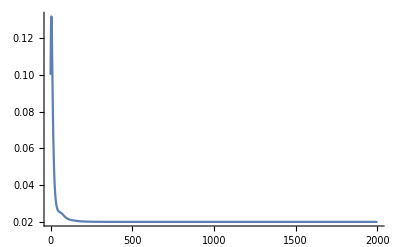

```mathematica
Plot[Evaluate[P3[t]/.soln1],{t,0,TT},PlotRange->All]
```

Solution #2: gives a biologially UNreasonable solution with a high parasite biomass

{{0.10168,0.0508399,0.14119,0.0110477,0.139652,1.26408}}

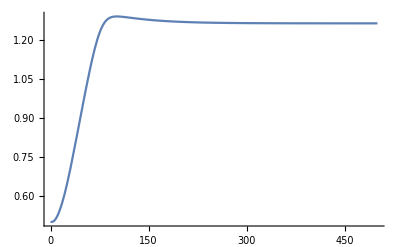

```mathematica
soln2=NDSolve[({G'[t]==dG,
S'[t]==dS,
Cc'[t]==dCc,
R'[t]==dR,
Ii'[t]==dIi,
P3'[t]==dP3,
G[0]==0.01,Cc[0]==0.01,S[0]==0.01,R[0]==0.01,Ii[0]==0.01,P3[0]==0.5}/.pars), {G,Cc,S,R,Ii,P3},{t,0,TT}];
{G[TT],Cc[TT],S[TT],R[TT],Ii[TT],P3[TT]}/.soln2
Plot[Evaluate[P3[t]/.soln2],{t,0,500},PlotRange->All]
```

Can I solve this analytically?

```mathematica
Srate=3 γ (α^(1/3) Smax^(1/3) S^(2/3)-S);
Ic=c (S+R);
(* maintenance cost for induced immune cells *)
M=mw (S+R)+mc Ic+mI Ii; 

(* State variable dynamics *)
dG=Imax S^(2/3) F-ρ G;
dS=Srate-(σ P3 S)/(hS+S);
dR=eR (ρ eA G-M-eG Srate-b R P3);
dIi=eI b R P3-muI Ii;
dP3=eP (σ P3 S)/(hS+S)-muP P3-nuC Ic P3-nuI Ii P3;
```

```mathematica
Solve[{dG==0,dS==0,dR==0,dIi==0,dP3==0}/.pars,{G,W,R,Ii,P3}]
```

$Aborted

```mathematica
Srate=3 γ (α^(1/3) Smax^(1/3) S^(2/3)-S);
Ic=c (S+R);
(* maintenance cost for induced immune cells *)
M=mw (S+R)+mc Ic+mI Ii; 

(* State variable dynamics *)
dG=Imax S^(2/3) F-ρ G;
dS=Srate-σ P3 S;
dR=eR (ρ eA G-M-eG Srate-b R P3);
dIi=eI b R P3-muI Ii;
dP3=eP σ P3 S-muP P3-nuC Ic P3-nuI Ii P3;
```

```mathematica
SequilP3=Solve[dS==0,S]
GequilP3=Solve[dG==0,G]/.SequilP3[[2]]

RequilP3Ii=Solve[dR==0,R]/.SequilP3[[2]]/.GequilP3[[1]]
IiequilP3=Solve[(dIi/.RequilP3Ii[[1]])==0,Ii]
RequilP3=RequilP3Ii/.IiequilP3[[1]]
```

{{S→0},{S→(27 Smax α γ^3)/(3 γ+P3 σ)^3}}

{{G→(9 F Imax ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3))/ρ}}

{{R→1/(c mc+mw+b P3)(-Ii mI+9 eA F Imax ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3)-27 eG Smax^(1/3) α^(1/3) γ ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3)-(27 c mc Smax α γ^3)/(3 γ+P3 σ)^3-(27 mw Smax α γ^3)/(3 γ+P3 σ)^3+(81 eG Smax α γ^4)/(3 γ+P3 σ)^3)}}

{{Ii→1/(-muI-(b eI mI P3)/(c mc+mw+b P3))(-(9 b eA eI F Imax P3 ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3))/(c mc+mw+b P3)+(27 b eG eI P3 Smax^(1/3) α^(1/3) γ ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3))/(c mc+mw+b P3)+(27 b c eI mc P3 Smax α γ^3)/((c mc+mw+b P3) (3 γ+P3 σ)^3)+(27 b eI mw P3 Smax α γ^3)/((c mc+mw+b P3) (3 γ+P3 σ)^3)-(81 b eG eI P3 Smax α γ^4)/((c mc+mw+b P3) (3 γ+P3 σ)^3))}}

{{R→1/(c mc+mw+b P3)(9 eA F Imax ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3)-27 eG Smax^(1/3) α^(1/3) γ ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3)-(27 c mc Smax α γ^3)/(3 γ+P3 σ)^3-(27 mw Smax α γ^3)/(3 γ+P3 σ)^3+(81 eG Smax α γ^4)/(3 γ+P3 σ)^3-1/(-muI-(b eI mI P3)/(c mc+mw+b P3))mI (-(9 b eA eI F Imax P3 ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3))/(c mc+mw+b P3)+(27 b eG eI P3 Smax^(1/3) α^(1/3) γ ((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3))/(c mc+mw+b P3)+(27 b c eI mc P3 Smax α γ^3)/((c mc+mw+b P3) (3 γ+P3 σ)^3)+(27 b eI mw P3 Smax α γ^3)/((c mc+mw+b P3) (3 γ+P3 σ)^3)-(81 b eG eI P3 Smax α γ^4)/((c mc+mw+b P3) (3 γ+P3 σ)^3)))}}

```mathematica
Solve[(Assuming[γ>0&&P3>0&&σ>0&&Smax>0,Expand[(dP3/.RequilP3[[1]]/.IiequilP3[[1]]/.SequilP3[[1]])]]/.((Smax α γ^3)/(3 γ+P3 σ)^3)^(2/3)->((Smax^(2/3) α^(2/3) γ^2)/(3 γ+P3 σ)^2))==0,P3]
```

$Aborted

This approach failed. Back up and try again.

#### Model with parasitizable and non-parasitizable structure

When you have structure that is non-parasitizable, then it will eventually run out to its equilibrium value, S_NPmax, so it is probably easier to just exclude that from the dynamics initially.

```mathematica
SNPrate=3 γ (α^(1/3) SNPmax^(1/3) SNP[t]^(2/3)-SNP[t]);
SPrate=3 γ (α^(1/3) SPmax^(1/3) SP[t]^(2/3)-SP[t]);
Ic=c (SNP[t]+SP[t]+R[t]);
(* maintenance cost for induced immune cells *)
M=mw (SNP[t]+SP[t]+R[t])+mc Ic+mI Ii[t]; 

(* State variable dynamics *)
dG=Imax (SNP[t]+SP[t])^(2/3) F-ρ G[t];
dSNP=SNPrate;
dSP=SPrate-(σ P3[t] SP[t])/(hS+SP[t]);
dCc=ρ (1-eA) G[t]-ρ Cc[t];
dR=eR (ρ eA G[t]-M-eG (SNPrate+SPrate)-b R[t] P3[t]);
dIi=eI b R[t] P3[t]-muI Ii[t];
dP3=(eP σ P3[t] SP[t])/(hS+SP[t])-muP P3[t]-nuC Ic P3[t]-nuI Ii[t] P3[t];
```

```mathematica
TT=1000;
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,SNPmax->0,SPmax->25,F->1.5,Imax->0.5,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.25,eP->0.5,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
(* Solution 1 gives a biologically reasonable solution with low parasite biomass *)
soln1=NDSolve[({G'[t]==dG,SNP'[t]==dSNP,SP'[t]==dSP,R'[t]==dR,
Ii'[t]==dIi,P3'[t]==dP3,
G[0]==1,SNP[0]==0,SP[0]==10,R[0]==3,Ii[0]==0.001,P3[0]==0.001}/.pars), 
{G,SNP,SP,R,Ii,P3},
{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Solution 2 gives a biologically UNreasonable solution with high parasite biomass *)
soln2=NDSolve[({G'[t]==dG,SNP'[t]==dSNP,SP'[t]==dSP,R'[t]==dR,
Ii'[t]==dIi,P3'[t]==dP3,
G[0]==0.001,SNP[0]==0,SP[0]==0.001,R[0]==0.001,Ii[0]==0.001,P3[0]==2}/.pars), 
{G,SNP,SP,R,Ii,P3},
{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{G[TT],SNP[TT],SP[TT],R[TT],Ii[TT],P3[TT]}/.soln1
{G[TT],SNP[TT],SP[TT],R[TT],Ii[TT],P3[TT]}/.soln2
```

{{3.18568,0.,24.7603,5.96614,1.18632,0.0198842}}

{{0.10168,0.,0.14119,0.0110477,0.139652,1.26408}}

{{0.0315972,0.,0.0244591,0.0040295,0.0449013,1.11528}}

{{0.0317277,0.,0.0246101,0.00405154,0.0450869,1.11301}}

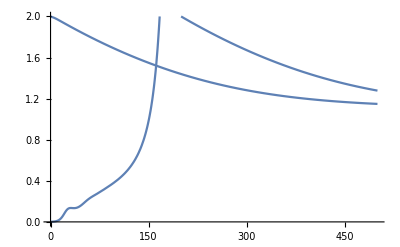

```mathematica
TT=1000;maxSP=25;
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,SNPmax->25-maxSP,SPmax->maxSP,F->1.5,Imax->0.5,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.5,eP->0.5,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
(* Solution 1 gives a biologically reasonable solution with low parasite biomass *)
soln1=NDSolve[({G'[t]==dG,SNP'[t]==dSNP,SP'[t]==dSP,R'[t]==dR,
Ii'[t]==dIi,P3'[t]==dP3,
G[0]==1,SNP[0]==SNPmax,SP[0]==maxSP/2,R[0]==3,Ii[0]==0.001,P3[0]==0.001}/.pars), 
{G,SNP,SP,R,Ii,P3},
{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Solution 2 gives a biologically UNreasonable solution with high parasite biomass *)
soln2=NDSolve[({G'[t]==dG,SNP'[t]==dSNP,SP'[t]==dSP,R'[t]==dR,
Ii'[t]==dIi,P3'[t]==dP3,
G[0]==0.001,SNP[0]==SNPmax,SP[0]==maxSP/20000,R[0]==0.001,Ii[0]==0.001,P3[0]==2}/.pars), 
{G,SNP,SP,R,Ii,P3},
{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{G[TT],SNP[TT],SP[TT],R[TT],Ii[TT],P3[TT]}/.soln1
{G[TT],SNP[TT],SP[TT],R[TT],Ii[TT],P3[TT]}/.soln2
Pl1=Plot[P3[t]/.soln1,{t,0,500},PlotRange->{{0,500},{0,2}}];
Pl2=Plot[P3[t]/.soln2,{t,0,500},PlotRange->{{0,500},{0,2}}];
Show[Pl1,Pl2]
```

When you have structure that is non-parasitizable, then it will eventually run out to its equilibrium value, S_NPmax, so it is probably easier to just exclude that from the dynamics initially and assume you have already reached whatever that equilibrium is.

Can you still get the existence of 2 equilibria under this circumstance?

```mathematica
SPrate=3 γ (α^(1/3) SPmax^(1/3) SP[t]^(2/3)-SP[t]);
Ic=c (SNPmax+SP[t]+R[t]);
(* maintenance cost for induced immune cells *)
M=mw (SNPmax+SP[t]+R[t])+mc Ic+mI Ii[t]; 

(* State variable dynamics *)
dG=Imax (SNPmax+SP[t])^(2/3) F-ρ G[t];
dSP=SPrate-(σ P3[t] SP[t])/(hS+SP[t]);
dCc=ρ (1-eA) G[t]-ρ Cc[t];
dR=eR (ρ eA G[t]-M-eG SPrate-b R[t] P3[t]);
dIi=eI b R[t] P3[t]-muI Ii[t];
dP3=(eP σ P3[t] SP[t])/(hS+SP[t])-muP P3[t]-nuC Ic P3[t]-nuI Ii[t] P3[t];
```

{{3.18568,24.7603,5.96614,1.18632,0.0198842}}

{{0.10168,0.14119,0.0110477,0.139652,1.26408}}

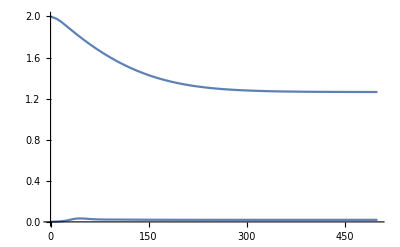

```mathematica
TT=1000;maxSP=25;
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,SNPmax->25-maxSP,SPmax->maxSP,F->1.5,Imax->0.5,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.25,eP->0.5,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
(* Solution 1 gives a biologically reasonable solution with low parasite biomass *)
soln1=NDSolve[({G'[t]==dG,SP'[t]==dSP,R'[t]==dR,
Ii'[t]==dIi,P3'[t]==dP3,
G[0]==1,SP[0]==10,R[0]==3,Ii[0]==0.001,P3[0]==0.001}/.pars), 
{G,SP,R,Ii,P3},
{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Solution 2 gives a biologically UNreasonable solution with high parasite biomass *)
soln2=NDSolve[({G'[t]==dG,SP'[t]==dSP,R'[t]==dR,
Ii'[t]==dIi,P3'[t]==dP3,
G[0]==0.001,SP[0]==0.001,R[0]==0.001,Ii[0]==0.001,P3[0]==2}/.pars), 
{G,SP,R,Ii,P3},
{t,0,TT},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{G[TT],SP[TT],R[TT],Ii[TT],P3[TT]}/.soln1
{G[TT],SP[TT],R[TT],Ii[TT],P3[TT]}/.soln2
Pl1=Plot[P3[t]/.soln1,{t,0,500},PlotRange->{{0,500},{0,2}}];
Pl2=Plot[P3[t]/.soln2,{t,0,500},PlotRange->{{0,500},{0,2}}];
Show[Pl1,Pl2]
```

### Analytical results with P_2 parasites

#### Nonlinear functional response

```mathematica
Srate=3 γ (Smax^(1/3) S^(2/3)-S);
Ic=c (S+R);
(* maintenance cost for induced immune cells *)
M=mw (S+R)+mc Ic+mI Ii; 

(* State variable dynamics *)
dG=(Imax S^(2/3) F)/(1+Exp[η (R/S-θ)])-ρ G;
dC=ρ (1-eA) G-ρ Cc-(σ P2 Cc)/(hC+Cc);
dS=Srate;
dR=eR (ρ eA G-M-eG Srate-b R P2);
dIi=eI b R P2-muI Ii;
dP3=eP (σ P2 Cc)/(hCc+Cc)-muP P2-nuC Ic P2-nuI Ii P2;
```

But, in this model, eventually S will reach S_max and growth will stop. Since we are interested in long-run behavior anyway, we might as well start the analysis assuming we are in that state.

```mathematica
Solve[Srate==0,S]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{S→0},{S→Smax}}

This also allows us a simplification of the dynamics of food in the gut, as ingestion will be constant as well.

The question is how much insight we can get into the condition dependent ingestion case. Let’s start with the simpler case first, and then work towards that case. If ingestion is condition-independent, we can simplify all of ingestion to a single term, which I will call ϕ, so ϕ=I_max S_max^(2/3)F. This allows me to immediately find the equilibrium gut contents, G^*=ϕ/ρ, and I can drop that equation as well. And, in the equations for the dynamics of C and R we can replace ρ G with ϕ. 

The dynamics of the system are:

```mathematica
Ic=c (Smax+R);
(* maintenance cost for induced immune cells *)
M=mw (Smax+R)+mc Ic+mI Ii; 
dC=(1-eA) ϕ-ρ Cc-(σ P2 Cc)/(hC+Cc);
dR=eR (eA ϕ-M-b R P2);
dIi=eI b R P2-muI Ii;
dP2=eP (σ P2 Cc)/(hC+Cc)-muP P2-nuC Ic P2-nuI Ii P2;
```

```mathematica
Iiequil=Solve[dIi==0,Ii][[1]]
```

{Ii→(b eI P2 R)/muI}

```mathematica
Requil=Solve[(dR/.Iiequil)==0,R][[1]]
```

{R→-(muI (c mc Smax+mw Smax-eA ϕ))/(c mc muI+muI mw+b eI mI P2+b muI P2)}

```mathematica
Ccequil=Solve[(dP2/.Iiequil/.Requil)==0,Cc][[1]]
```

{Cc→-((hC (c mc muI muP+muI muP mw+b eI mI muP P2+b muI muP P2+b c eI mI nuC P2 Smax+b c muI nuC P2 Smax-b c eI mc nuI P2 Smax-b eI mw nuI P2 Smax+c eA muI nuC ϕ+b eA eI nuI P2 ϕ))/(c mc muI muP+muI muP mw+b eI mI muP P2+b muI muP P2+b c eI mI nuC P2 Smax+b c muI nuC P2 Smax-b c eI mc nuI P2 Smax-b eI mw nuI P2 Smax-c eP mc muI σ-eP muI mw σ-b eI eP mI P2 σ-b eP muI P2 σ+c eA muI nuC ϕ+b eA eI nuI P2 ϕ))}

Although I cannot explicitly write down the equation for the P_2 equilibrium, you can see that it is a cubic equation, which means that there will be three equilibria. Whether they are all biologically feasible is unclear, and whether you can get multiple equilibria to be stable is also unclear.

```mathematica
P2equil=Collect[Numerator[Together[dC/.Solve[(dP2/.Solve[dIi==0,Ii][[1]]/.Solve[(dR/.Solve[dIi==0,Ii][[1]])==0,R][[1]])==0,Cc][[1]]]],P2];part1=Simplify[P2equil[[1;;21]]]
part2=Simplify[P2equil[[22]]]
part3=Simplify[P2equil[[23]]]
part4=Simplify[P2equil[[24]]]
```

-eP muI^2 (c mc+mw) (mw (hC muP ρ-(-1+eA) (muP-eP σ) ϕ)+c (hC ρ (mc muP+eA nuC ϕ)-(-1+eA) ϕ (mc muP-eP mc σ+eA nuC ϕ)))

muI P2 (c^2 (eA^2 muI nuC^2 ϕ^2-mc nuC (eA muI (-2 muP+eP σ) ϕ+b eP (eI mI+muI) Smax (hC ρ+ϕ-eA ϕ))+mc^2 (muI muP (muP-eP σ)+b eI eP nuI Smax (hC ρ+ϕ-eA ϕ)))+mw (b eI eP (hC ρ (-2 mI muP+mw nuI Smax-eA nuI ϕ)+(-1+eA) ϕ (2 mI muP-mw nuI Smax-2 eP mI σ+eA nuI ϕ))+muI (muP^2 mw-2 b (-1+eA) eP^2 σ ϕ-eP muP (mw σ+2 b (hC ρ+ϕ-eA ϕ))))+c (-nuC (eA muI mw (-2 muP+eP σ) ϕ+b eP (eI mI+muI) (hC ρ+ϕ-eA ϕ) (mw Smax+eA ϕ))+mc (-b eI eP (hC ρ (2 mI muP-2 mw nuI Smax+eA nuI ϕ)-(-1+eA) ϕ (2 mI muP-2 mw nuI Smax-2 eP mI σ+eA nuI ϕ))+2 muI (muP^2 mw-b (-1+eA) eP^2 σ ϕ-eP muP (mw σ+b (hC ρ+ϕ-eA ϕ))))))

b P2^2 (c^2 muI (eI mI nuC+muI nuC-eI mc nuI) Smax (2 mc muP-eP mc σ+2 eA nuC ϕ)-b eI^2 eP mI (hC ρ (mI muP-mw nuI Smax+eA nuI ϕ)-(-1+eA) ϕ (-mw nuI Smax+mI (muP-eP σ)+eA nuI ϕ))+muI^2 (2 muP^2 mw-b (-1+eA) eP^2 σ ϕ-eP muP (2 mw σ+b (hC ρ+ϕ-eA ϕ)))+eI muI (-nuI (mw Smax-eA ϕ) (2 muP mw-eP (mw σ+b (hC ρ+ϕ-eA ϕ)))+2 mI (muP^2 mw-b (-1+eA) eP^2 σ ϕ-eP muP (mw σ+b (hC ρ+ϕ-eA ϕ))))+c (-b eI^2 eP mI (mI nuC-mc nuI) Smax (hC ρ+ϕ-eA ϕ)+muI^2 (2 mc muP (muP-eP σ)+nuC (2 muP (mw Smax+eA ϕ)-eP (b Smax (hC ρ+ϕ-eA ϕ)+σ (mw Smax+eA ϕ))))+eI muI (mc (2 mI muP (muP-eP σ)+nuI (muP (-4 mw Smax+2 eA ϕ)+eP (σ (2 mw Smax-eA ϕ)+b Smax (hC ρ+ϕ-eA ϕ))))+nuC (2 eA nuI ϕ (-mw Smax+eA ϕ)+mI (2 muP (mw Smax+eA ϕ)-eP (2 b Smax (hC ρ+ϕ-eA ϕ)+σ (mw Smax+eA ϕ)))))))

b^2 P2^3 (muI (muP+c nuC Smax)+eI (mI (muP+c nuC Smax)-nuI (c mc Smax+mw Smax-eA ϕ))) (muI (muP+c nuC Smax-eP σ)+eI (mI (muP+c nuC Smax-eP σ)-nuI (c mc Smax+mw Smax-eA ϕ)))

Parameters - plug ‘em in and check out whether the equilibria are all feasible:

```mathematica
pars={ϕ->Imax maxS^(2/3) F,mw->0.09,ρ->2,α->1,eA->0.5,eR->1,c->0.00005,mc->0.2,mI->0.3,eI->1,b->0.5,muI->0.05,σ->0.25,eP->0.5,hC->1,muP->0.0015,nuC->0.01,nuI->0.1,Smax->maxS}/.{Imax->0.5,maxS->25,F->1.5};
Solve[(P2equil/.pars)==0,P2]
Ccequil/.pars/.Solve[(P2equil/.pars)==0,P2]
Requil/.pars/.Solve[(P2equil/.pars)==0,P2]
Iiequil/.Requil/.pars/.Solve[(P2equil/.pars)==0,P2]
```

{{P2→-0.0256481},{P2→0.00981567},{P2→12.5566}}

{{Cc→-0.998769},{Cc→1.60235},{Cc→-1.83845}}

{{R→3955.4},{R→7.6867},{R→0.0217075}}

{{Ii→-1014.49},{Ii→0.754501},{Ii→2.72572}}

Check for stability of each of the three sets of equilibria:

```mathematica
J={{D[dC,Cc],D[dC,R],D[dC,Ii],D[dC,P2]},
{D[dR,Cc],D[dR,R],D[dR,Ii],D[dR,P2]},
{D[dIi,Cc],D[dIi,R],D[dIi,Ii],D[dIi,P2]},
{D[dP2,Cc],D[dP2,R],D[dP2,Ii],D[dP2,P2]}};
Eigenvalues[J/.Iiequil/.Requil/.Ccequil/.pars/.Solve[(P2equil/.pars)==0,P2][[1]]]
Eigenvalues[J/.Iiequil/.Requil/.Ccequil/.pars/.Solve[(P2equil/.pars)==0,P2][[2]]]
Eigenvalues[J/.Iiequil/.Requil/.Ccequil/.pars/.Solve[(P2equil/.pars)==0,P2][[3]]]
```

{4127.51,104.102,-0.146308,-0.0308142}

{-2.00035+0. ⅈ,-0.0716222+0. ⅈ,-0.0366548+0.0582976 ⅈ,-0.0366548-0.0582976 ⅈ}

{-6.27223,-6.05001,-0.367658,-0.193727}

Numerically confirm that these are indeed attainable equilibria:

```mathematica
Ic=c (Smax+R[t]);
(* maintenance cost for induced immune cells *)
M=mw (Smax+R[t])+mc Ic+mI Ii[t];
dCdt=(1-eA) ϕ-ρ Cc[t]-(σ P2[t] Cc[t])/(hC+Cc[t]);
dRdt=eR (eA ϕ-M-b R[t] P2[t]);
dIidt=eI b R[t] P2[t]-muI Ii[t];
dP2dt=eP (σ P2[t] Cc[t])/(hC+Cc[t])-muP P2[t]-nuC Ic P2[t]-nuI Ii[t] P2[t];
sol=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==1.6,R[0]==7,Ii[0]==0.5,P2[0]==0.01}/.pars),{Cc,R,Ii,P2},{t,0,1000}];
{Cc[1000],R[1000],Ii[1000],P2[1000]}/.sol
```

{{1.60235,7.6867,0.754501,0.00981567}}

The key equilibrium appears to be C, as the two stable equilibrium points differ in the sign of the C equilibrium but no others. Can I come up with a simple expression for Ĉ that determines when it is positive versus negative?

```mathematica
Solve[dC==0,Cc]/.pars
Solve[dC==0,Cc]/.pars
Solve[dC==0,Cc]/.pars/.Solve[(P2equil/.pars)==0,P2][[1]]
Solve[dC==0,Cc]/.pars/.Solve[(P2equil/.pars)==0,P2][[2]]
Solve[dC==0,Cc]/.pars/.Solve[(P2equil/.pars)==0,P2][[3]]
```

{{Cc→1/4 (1.2062+√(25.6496+(1.2062-0.25 P2)^2)-0.25 P2)},{Cc→1/4 (1.2062-√(25.6496+(1.2062-0.25 P2)^2)-0.25 P2)}}

{{Cc→1/4 (1.2062+√(25.6496+(1.2062-0.25 P2)^2)-0.25 P2)},{Cc→1/4 (1.2062-√(25.6496+(1.2062-0.25 P2)^2)-0.25 P2)}}

{{Cc→1.60508},{Cc→-0.998769}}

{{Cc→1.60235},{Cc→-1.00047}}

{{Cc→0.871985},{Cc→-1.83845}}

Instability of the parasite-free equilibrium requires (ϵ_P σ Ĉ)/(h_C+Ĉ)>μ_P-ν_i OverHat[I_i]-ν_c c(S_max+R̂), where Ĉ, OverHat[I_i] and R̂ are the parasite-free equilibria. At that equilibrium, OverHat[I_i]=0 and Ĉ=((1-ϵ_A)ϕ)/ρ. This is actually an interesting condition, for the following reason: on the one hand, it seems like it should be impossible for bistability involving a stable parasite-free equilibrium and a stable endemic equilibrium because, when the system has reached it’s parasite-free equilibrium, Ĉ is as large as it will ever be and OverHat[I_i] is as small as it will ever be. However, if the parasite-free equilibrium is stable because ν_C is very large, it might be possible to get bistability because R̂ is also very large at the parasite-free equilibrium - that is, if the parasite was introduced before R had reached this equilibrium, it might be possible for it to invade and go towards a stable endemic equilibrium.

```mathematica
(* Calculate stability condition for the parasite-free equilibrium using NGT *)
Fmat={{0,0,0,0},{0,0,0,0},{0,0,0,b eI R},{0,0,0,(Cc eP σ)/(Cc+hC)}};
Gmat={{ρ,0,0,(Cc σ)/(Cc+hC)},{0,eR (c mc+mw),eR mI,b eR R},{0,0,muI,0},{0,0,0,muP+Ii nuI+c nuC (R+Smax)}};
(J/.{P2->0})==Fmat-Gmat//Simplify
Eigenvalues[Dot[Fmat,Inverse[Gmat]]]
```

True

{0,0,0,(Cc eP σ)/((Cc+hC) (muP+Ii nuI+c nuC R+c nuC Smax))}

The condition for stability of the parasite free equilibrium is that the quantity below be negative:

```mathematica
P2freecond=((Cc eP σ)/(Cc+hC)-(muP+Ii nuI+c nuC R+c nuC Smax)/.Solve[dR==0,R]/.Solve[(dC/.P2->0)==0,Cc]/.P2->0/.Ii->0)[[1,1]]
```

-muP-c nuC Smax-(c nuC (-c mc Smax-mw Smax+eA ϕ))/(c mc+mw)-((-1+eA) eP σ ϕ)/(ρ (hC-((-1+eA) ϕ)/ρ))

Now, a bit more thinking can help us here. In particular, an often lamented problem with this type of immune-parasite model is that there is no way for the immune system to eliminate the parasite because of the feedback between the immune system and the parasite: that is, as the parasite abundance gets low, the immune response decays, allowing the parasite to persist at a low level. It is impossible for the immune response to exclude the parasite without some kind of delay in its response to parasite abundance (see Jo Lello’s paper with Andy Fenton for an example). However, in this model, there is the possibility because of the fact that the constitutive response increases independent of the parasite because it grows as the parasite grows. Moreover, the induced respose may grow as well because it is dependent on the amount of reserve. This sets up the potential for some very interesting growth-by-food-by-immunity interactions in allowing for bistability. 

But let’s not get too far ahead of ourselves: I still need to demonstrate that it is actually possible to get bistability.

```mathematica
Ic=c (Smax+R[t]);
(* maintenance cost for induced immune cells *)
M=mw (Smax+R[t])+mc Ic+mI Ii[t];
dCdt=(1-(eA-(eAred P2[t])/(he+P2[t]))) ϕ-ρ Cc[t]-(σ P2[t] Cc[t])/(hC+Cc[t]);
dRdt=eR ((eA-(eAred P2[t])/(he+P2[t])) ϕ-M-b R[t] P2[t]);
dIidt=eI b R[t] P2[t]-muI Ii[t];
dP2dt=eP (σ P2[t] Cc[t])/(hC+Cc[t])-muP P2[t]-nuC Ic P2[t]-nuI Ii[t] P2[t];
```

ASIDE: It may also be necessary to reintroduce the dynamics of structure. These will not affect the parasite invasion condition because Ŝ=S_max, but might affect the stability of the endemic equilibrium in a way that would benefit the parasite (because, again, if the parasite is introduced before S=S_max, it might benefit from the lowered constuitive immune defense. I can also consider adding back in the parasite abundance-dependent reduction in assimilation efficiency, which would increase C to a level that is beyond what it would normally be able to achieve, but would again not affect the parasite invasion condition (since that is derived from assuming P=0, with assimilation efficiency equal to its normal level).

Here is a set of parameters that allow for bistability and produce a reasonably accurate endemic equilibrium! Of course, they require that the parasite is very good at reducing the assimilation efficiency.

-0.0418461

{{1.68254,8.28564,0.0452073,0.00109122}}

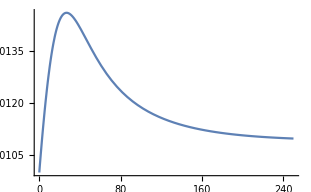

{{0.801551,27.8495,5.7683×10^-16,2.3991×10^-18}}

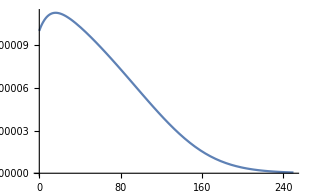

```mathematica
pars={ϕ->Imax maxS^(2/3) F,mw->0.09,ρ->2,α->1,eA->0.75,eR->1,c->0.005,mc->0.2,mI->0.3,eI->1,b->0.5,muI->0.1,σ->0.25,eP->0.75,hC->0.1,muP->0.05,nuC->0.6,nuI->0.6,Smax->maxS,eAred->0.3,he->0.0001}/.{Imax->0.5,maxS->25,F->1.5};
P2freecond/.pars
sol1=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==2,R[0]==5,Ii[0]==0,P2[0]==0.001}/.pars),{Cc,R,Ii,P2},{t,0,10000}];
{Cc[10000],R[10000],Ii[10000],P2[10000]}/.sol1
Plot[P2[t]/.sol1,{t,0,250},PlotRange->All]
sol2=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==2,R[0]==10,Ii[0]==0,P2[0]==0.0001}/.pars),{Cc,R,Ii,P2},{t,0,10000}];
{Cc[10000],R[10000],Ii[10000],P2[10000]}/.sol2
Plot[P2[t]/.sol2,{t,0,250},PlotRange->All]
```

-0.00779181

{{1.70221,8.2398,0.0268043,0.000406629}}

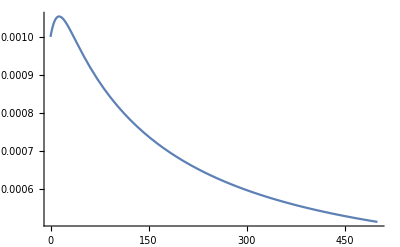

{{0.801551,28.3478,4.09987×10^-13,1.66698×10^-15}}

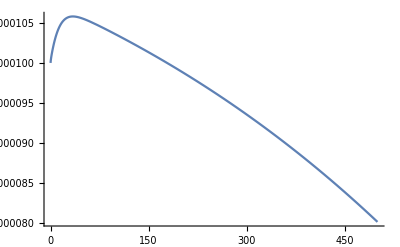

```mathematica
pars={ϕ->Imax maxS^(2/3) F,mw->0.09,ρ->2,α->1,eA->0.75,eR->1,c->0.0005,mc->0.3,mI->0.3,eI->0.8,b->1,muI->0.1,σ->0.1,eP->0.8,hC->0.3,muP->0.05,nuC->0.6,nuI->0.3,Smax->maxS,eAred->0.35,he->0.0001}/.{Imax->0.5,maxS->25,F->1.5};
P2freecond/.pars
sol1=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==2,R[0]==5,Ii[0]==0,P2[0]==0.001}/.pars),{Cc,R,Ii,P2},{t,0,10000}];
{Cc[10000],R[10000],Ii[10000],P2[10000]}/.sol1
Plot[P2[t]/.sol1,{t,0,500},PlotRange->All]
sol2=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==2,R[0]==10,Ii[0]==0,P2[0]==0.0001}/.pars),{Cc,R,Ii,P2},{t,0,10000}];
{Cc[10000],R[10000],Ii[10000],P2[10000]}/.sol2
Plot[P2[t]/.sol2,{t,0,500},PlotRange->All]
```

What happens if I add condition-dependent feeding back into the model?

{-0.0106868}

{{1.90874,1.73604,0.0370442,0.00266728}}

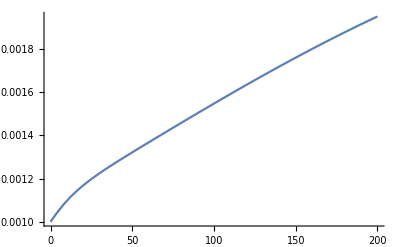

{{0.463595,5.85488,-1.68202×10^-15,-3.2073×10^-17}}

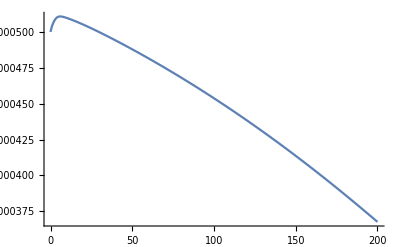

```mathematica
pars={mw->0.09,ρ->2,α->1,eA->0.75,eR->1,c->0.0005,mc->0.3,mI->0.3,eI->0.8,b->1,muI->0.1,σ->0.1,eP->0.8,hC->0.3,muP->0.05,nuC->0.6,nuI->0.3,Smax->25,eAmin->0.5,he->0.0001,Imax->0.5,F->1.5,η->20,θ->0.25};

(* Calculate the parasite-free equilibrium values of C and R *)
M0=(mw+mc c) (Smax+R[t]);
dCdt0=(1-eA(1-(eAmin P2[t])/(he+P2[t]))) (Imax Smax^(2/3) F)/(1+Exp[η (R[t]/Smax-θ)])-ρ Cc[t]-(σ P2[t] Cc[t])/(hC+Cc[t])/.P2[t]->0;
dRdt0=eR (eA(1-(eAmin P2[t])/(he+P2[t])) (Imax Smax^(2/3) F)/(1+Exp[η (R[t]/Smax-θ)])-M0-b R[t] P2[t])/.P2[t]->0;
sol0=NDSolve[({Cc'[t]==dCdt0,R'[t]==dRdt0,Cc[0]==2,R[0]==5}/.pars),{Cc,R},{t,0,10000}];
{Cc[10000],R[10000]}/.sol0;

(* Calculate the parasite invasion criterion at this equilibrium *)
P2freecond/.ϕ->(Imax Smax^(2/3) F)/(1+Exp[η (R/Smax-θ)])/.pars/.R->(R[10000]/.sol0)

(* Simulate the system with the parasite *)
Ic=c (Smax+R[t]);
M=mw (Smax+R[t])+mc Ic+mI Ii[t];
dCdt=(1-eA(1-(eAmin P2[t])/(he+P2[t]))) (Imax Smax^(2/3) F)/(1+Exp[η (R[t]/Smax-θ)])-ρ Cc[t]-(σ P2[t] Cc[t])/(hC+Cc[t]);
dRdt=eR (eA(1-(eAmin P2[t])/(he+P2[t])) (Imax Smax^(2/3) F)/(1+Exp[η (R[t]/Smax-θ)])-M-b R[t] P2[t]);
dIidt=eI b R[t] P2[t]-muI Ii[t];
dP2dt=eP (σ P2[t] Cc[t])/(hC+Cc[t])-muP P2[t]-nuC Ic P2[t]-nuI Ii[t] P2[t];
sol1=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==2,R[0]==1,Ii[0]==0,P2[0]==0.001}/.pars),{Cc,R,Ii,P2},{t,0,10000}];
{Cc[10000],R[10000],Ii[10000],P2[10000]}/.sol1
Plot[P2[t]/.sol1,{t,0,200},PlotRange->All]
sol2=NDSolve[({Cc'[t]==dCdt,R'[t]==dRdt,Ii'[t]==dIidt,P2'[t]==dP2dt,Cc[0]==2,R[0]==1,Ii[0]==0,P2[0]==0.00005}/.pars),{Cc,R,Ii,P2},{t,0,10000}];
{Cc[10000],R[10000],Ii[10000],P2[10000]}/.sol2
Plot[P2[t]/.sol2,{t,0,200},PlotRange->All]
```

#### Linear parasite functional response

```mathematica
Ic=c (Smax+R);
(* maintenance cost for induced immune cells *)
M=mw (Smax+R)+mc Ic+mI Ii; 
dC=(1-eA) ϕ-ρ Cc-σ P2 Cc;
dR=eR (eA ϕ-M-b R P2);
dIi=eI b R P2-muI Ii;
dP2=eP σ P2 Cc-muP P2-nuC Ic P2-nuI Ii P2;
```

```mathematica
Solve[dIi==0,Ii]
```

{{Ii→(b eI P2 R)/muI}}

```mathematica
Solve[(dR/.Solve[dIi==0,Ii][[1]])==0,R]
```

{{R→-(muI (c mc Smax+mw Smax-eA ϕ))/(c mc muI+muI mw+b eI mI P2+b muI P2)}}

```mathematica
Solve[(dP2/.Solve[dIi==0,Ii][[1]]/.Solve[(dR/.Solve[dIi==0,Ii][[1]])==0,R][[1]])==0,Cc]
```

{{Cc→(c mc muI muP+muI muP mw+b eI mI muP P2+b muI muP P2+b c eI mI nuC P2 Smax+b c muI nuC P2 Smax-b c eI mc nuI P2 Smax-b eI mw nuI P2 Smax+c eA muI nuC ϕ+b eA eI nuI P2 ϕ)/(eP (c mc muI+muI mw+b eI mI P2+b muI P2) σ)}}

With a linear functional response, you can only get two equilibria.

```mathematica
P2equil=Collect[Numerator[Together[dC/.Solve[(dP2/.Solve[dIi==0,Ii][[1]]/.Solve[(dR/.Solve[dIi==0,Ii][[1]])==0,R][[1]])==0,Cc][[1]]]],P2];
Simplify[P2equil[[1;;7]]]
Simplify[P2equil[[8]]]
Simplify[P2equil[[9]]]
```

-muI (mw (muP ρ+(-1+eA) eP σ ϕ)+c (eA nuC ρ ϕ+mc (muP ρ+(-1+eA) eP σ ϕ)))

-P2 (muI σ (c mc muP+muP mw+c eA nuC ϕ)+b (muI (muP ρ+c nuC Smax ρ+(-1+eA) eP σ ϕ)+eI (-nuI ρ (c mc Smax+mw Smax-eA ϕ)+mI (muP ρ+c nuC Smax ρ+(-1+eA) eP σ ϕ))))

-b P2^2 σ (muI (muP+c nuC Smax)+eI (mI (muP+c nuC Smax)-nuI (c mc Smax+mw Smax-eA ϕ)))

```mathematica
pars={mw->0.09,ρ->2,α->1,eA->0.5,eR->1,eG->1,c->0.00005,mc->0.2,mI->0.3,eI->1,γ->0.02,SNPmax->25-maxSP,SPmax->maxSP,F->1.5,Imax->0.5,η->10,θ->0.25,b->0.5,muI->0.05,σ->0.25,eP->0.5,hS->1,muP->0.0015,nuC->0.01,nuI->0.1};
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```